# Delovno aktivno prebivalstvo - izbrani kazalniki, kohezijski in statistične regije, Slovenija, letno

### Stopnja delovne aktivnosti

```mathematica
leta=Range[1993,2021]
```

{1993,1994,1995,1996,1997,1998,1999,2000,2001,2002,2003,2004,2005,2006,2007,2008,2009,2010,2011,2012,2013,2014,2015,2016,2017,2018,2019,2020,2021}

```mathematica
podatki1=Import[NotebookDirectory[]<>"tabela1_brezglave_vejica.csv", "Table","FieldSeparators"->",", HeaderLines->1, CharacterEncoding->"WindowsEastEurope"]//Transpose//ResourceFunction["DatasetWithHeaders"]//Map[If[#=="...",0,#]&,#,{2}]&;
```

```mathematica
tabStopnjaDelovneAktivnsti=podatki1//Transpose//Prepend["Leta"->leta]//Transpose
```

```mathematica
(*Samo tabela posebi za SLOVENIJA*)
```

```mathematica
slo=tabStopnjaDelovneAktivnsti//Query[All,{1,2}];
```

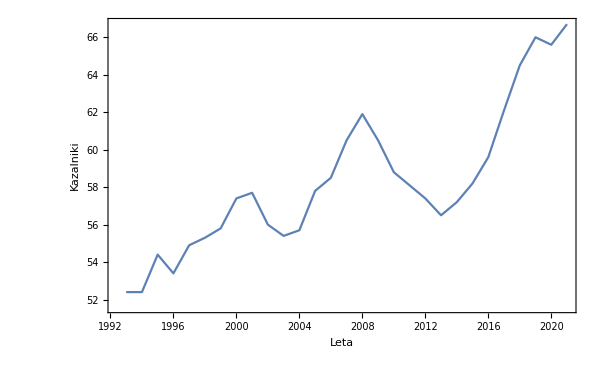

```mathematica
ListLinePlot[slo,Frame->True,FrameLabel->{{"Kazalniki",""},{"Leta","Stopnja delovne aktivnosti"}},BaseStyle->{FontSize->15},ImageSize->600]
```

```mathematica
samoVrednostiSlo=tabStopnjaDelovneAktivnsti//Query[All,{2,2}];
```

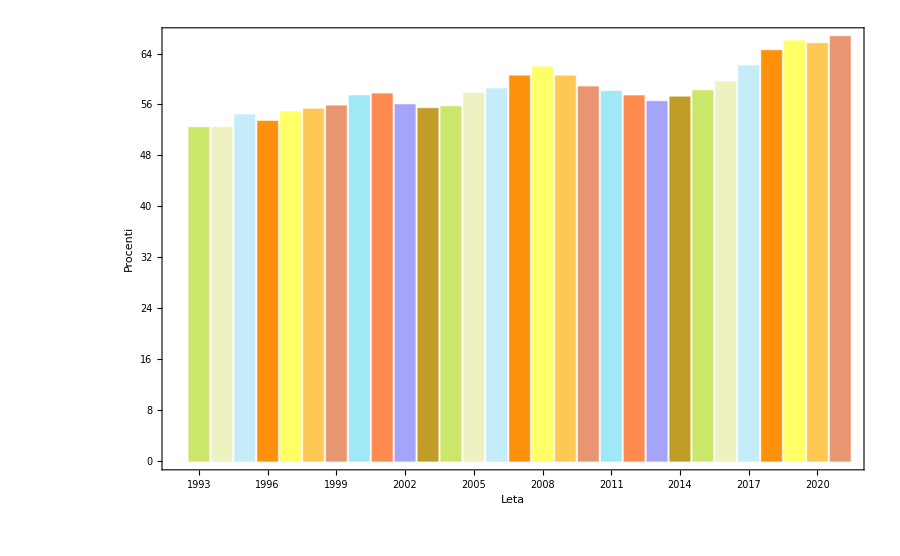

```mathematica
BarChart[Transpose[samoVrednostiSlo],ChartLabels->leta,ChartStyle->45,Frame->True,FrameLabel->{{"Procenti",""},{"Leta","Stopnja Delovne Aktivnosti"}},BaseStyle->{FontSize->10},ImageSize->900]
```

## Stopnja delovne aktivnosti za moške

```mathematica
podatki2=Import[NotebookDirectory[]<>"tabela2_brezglave_vejica.csv", "Table","FieldSeparators"->",", HeaderLines->1, CharacterEncoding->"WindowsEastEurope"]//Transpose//ResourceFunction["DatasetWithHeaders"]//Map[If[#=="...",0,#]&,#,{2}]&;
```

```mathematica
tabStopnjaDelovneAktivnostiMoski=podatki2//Transpose//Prepend["Leta"->leta]//Transpose
```

```mathematica
(*tabela posebi za SLOVENIJA*)
```

```mathematica
slo2=tabStopnjaDelovneAktivnostiMoski//Query[All,{1,2}];
```

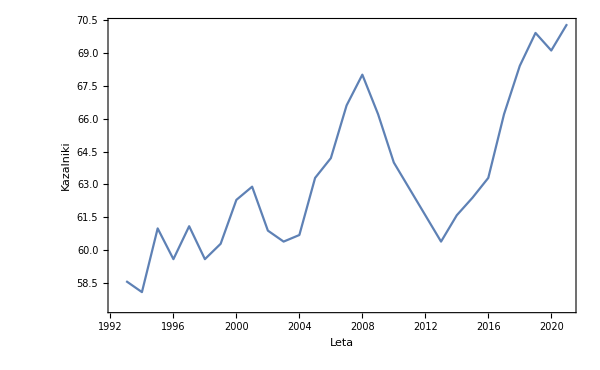

```mathematica
ListLinePlot[slo2,Frame->True,FrameLabel->{{"Kazalniki",""},{"Leta","Stopnja delovne aktivnosti za moške"}},BaseStyle->{FontSize->15},ImageSize->600]
```

```mathematica
samoVrednostiSlo2=tabStopnjaDelovneAktivnostiMoski//Query[All,{2,2}];
```

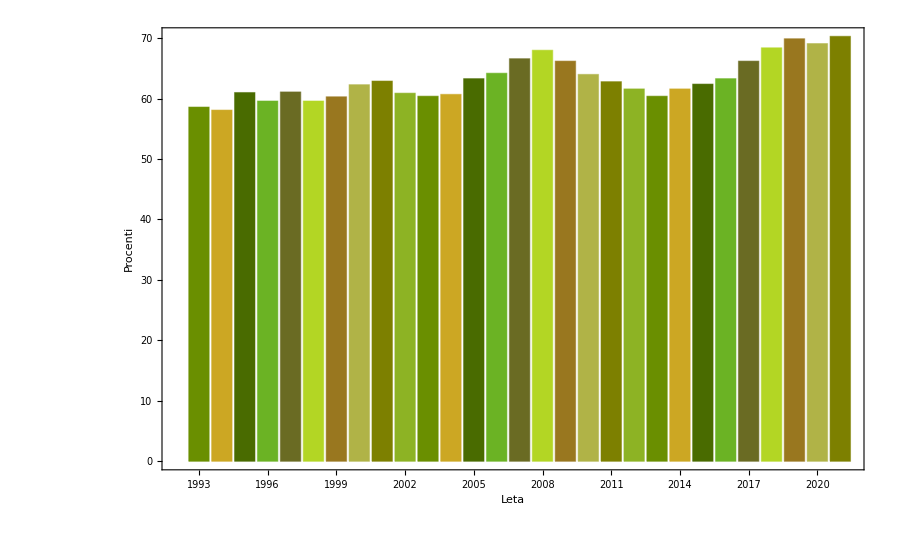

```mathematica
BarChart[Transpose[samoVrednostiSlo2],ChartLabels->leta,ChartStyle->78,Frame->True,FrameLabel->{{"Procenti",""},{"Leta","Stopnja Delovne Aktivnosti za moške"}},BaseStyle->{FontSize->10},ImageSize->900]
```

## Stopnja delovne aktivnosti za ženske

```mathematica
podatki3=Import[NotebookDirectory[]<>"tabela3_brezglave_vejica.csv", "Table","FieldSeparators"->",", HeaderLines->1, CharacterEncoding->"WindowsEastEurope"]//Transpose//ResourceFunction["DatasetWithHeaders"]//Map[If[#=="...",0,#]&,#,{2}]&;
```

```mathematica
tabStopnjaDelovneAktivnostiZenske=podatki3//Transpose//Prepend["Leta"->leta]//Transpose
```

```mathematica
(*tabela posebi za SLOVENIJA*)
```

```mathematica
slo3=tabStopnjaDelovneAktivnostiZenske//Query[All,{1,2}];
```

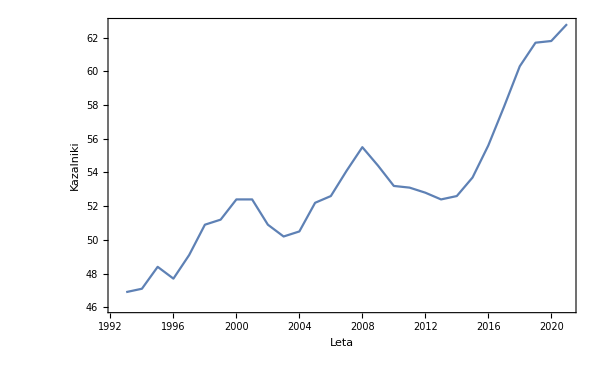

```mathematica
ListLinePlot[slo3,Frame->True,FrameLabel->{{"Kazalniki",""},{"Leta","Stopnja delovne aktivnosti za ženske"}},BaseStyle->{FontSize->15},ImageSize->600]
```

```mathematica
samoVrednostiSlo3=tabStopnjaDelovneAktivnostiZenske//Query[All,{2,2}];
```

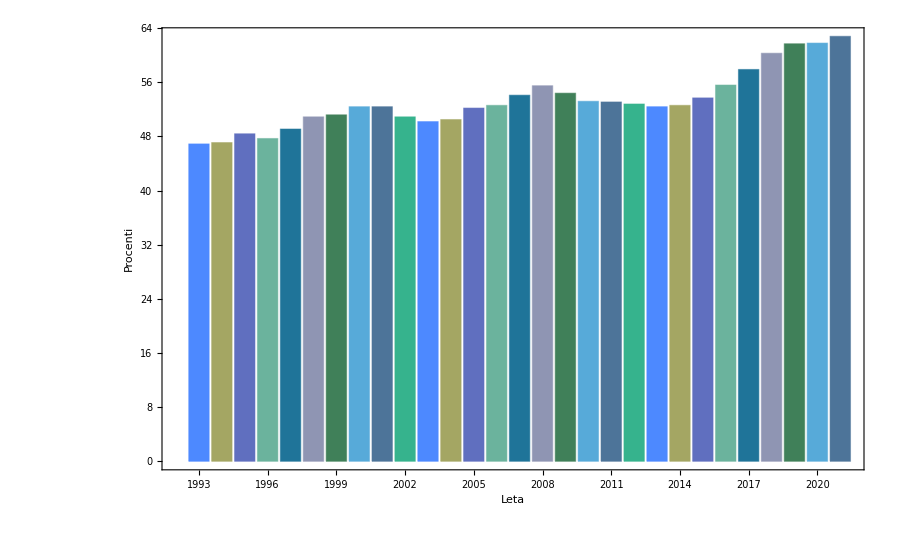

```mathematica
BarChart[Transpose[samoVrednostiSlo3],ChartLabels->leta,ChartStyle->66,Frame->True,FrameLabel->{{"Procenti",""},{"Leta","Stopnja Delovne Aktivnosti za moške"}},BaseStyle->{FontSize->10},ImageSize->900]
```